```mathematica
V= 10
h1=1
h2=10
h3 = 0.1
```

10

1

10

0.1

```mathematica
t11=0.5983079586971319
t21=0.5561393692990029
t31=0.9459116686858626
t12=0.30330746850629114
t22=0.5157925334824719
t32=0.6976716905130128
t13=1.0397846467067289
t23=0.7548947295581938
t33=0.9813791886198818
```

0.598308

0.556139

0.945912

0.303307

0.515793

0.697672

1.03978

0.754895

0.981379

```mathematica
rce1 = {x'[t]==V*Cos[β[t]]-(V/h1)y[t],y'[t]==V*Sin[β[t]],β'[t]==(V/h1)(Cos[β[t]])^2}
rce2 = {x'[t]==V*Cos[β[t]]-(V/h2)y[t],y'[t]==V*Sin[β[t]],β'[t]==(V/h2)(Cos[β[t]])^2}
rce3 = {x'[t]==V*Cos[β[t]]-(V/h3)y[t],y'[t]==V*Sin[β[t]],β'[t]==(V/h3)(Cos[β[t]])^2}
```

{x'[t]==10 Cos[β[t]]-10 y[t],y'[t]==10 Sin[β[t]],β'[t]==10 Cos[β[t]]^2}

{x'[t]==10 Cos[β[t]]-y[t],y'[t]==10 Sin[β[t]],β'[t]==Cos[β[t]]^2}

{x'[t]==10 Cos[β[t]]-100. y[t],y'[t]==10 Sin[β[t]],β'[t]==100. Cos[β[t]]^2}

```mathematica
sol11 = NDSolve[Join[rce1,{x[0]==5,y[0]==4,β[0]==4.9029388496394155}],{x,y,β},{t,0,3600}]
sol21 = NDSolve[Join[rce2,{x[0]==5,y[0]==4,β[0]==3.801725332795212}],{x,y,β},{t,0,3600}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],β→InterpolatingFunction[…]}}

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],β→InterpolatingFunction[…]}}

```mathematica
sol31  = NDSolve[Join[rce3,{x[0]==5,y[0]==4,β[0]==4.727246501369415}],{x,y,β},{t,0,3600}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],β→InterpolatingFunction[…]}}

```mathematica
sol12 =NDSolve[Join[rce1,{x[0]==5,y[0]==3,β[0]==4.528104805962796}],{x,y,β},{t,0,3600}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],β→InterpolatingFunction[…]}}

```mathematica
sol22 = NDSolve[Join[rce2,{x[0]==5,y[0]==3,β[0]==3.5831464526278474}],{x,y,β},{t,0,3600}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],β→InterpolatingFunction[…]}}

```mathematica
sol32 = NDSolve[Join[rce3,{x[0]==5,y[0]==3,β[0]==4.732429934220352}],{x,y,β},{t,0,3600}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],β→InterpolatingFunction[…]}}

```mathematica
sol13= NDSolve[Join[rce1,{x[0]==-5,y[0]==4,β[0]==4.849606813967257}],{x,y,β},{t,0,3600}]
sol23= NDSolve[Join[rce2,{x[0]==-5,y[0]==4,β[0]==5.4813269653835315}],{x,y,β},{t,0,3600}]
sol33= NDSolve[Join[rce3,{x[0]==-5,y[0]==4,β[0]==4.726865209087336}],{x,y,β},{t,0,3600}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],β→InterpolatingFunction[…]}}

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],β→InterpolatingFunction[…]}}

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],β→InterpolatingFunction[…]}}

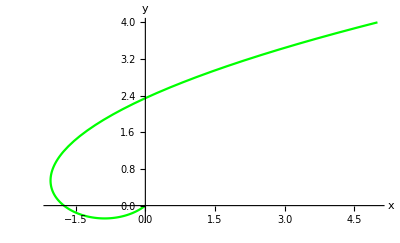

```mathematica
graf11  =ParametricPlot[Table[{x[t],y[t]}/.sol11],{t,0,t11},AxesLabel->{x,y},PlotRange->All,PlotStyle->{Green}]
```

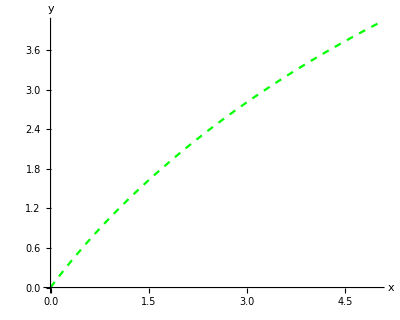

```mathematica
graf21  =ParametricPlot[Table[{x[t],y[t]}/.sol21],{t,0,t21},AxesLabel->{x,y},PlotRange->All,PlotStyle->{Green,Dashed}]
```

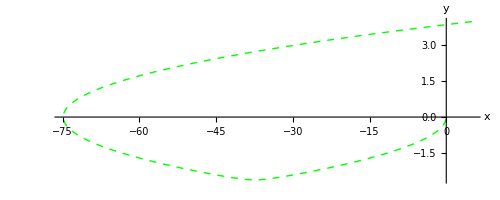

```mathematica
graf31  =ParametricPlot[Table[{x[t],y[t]}/.sol31],{t,0,t31},AxesLabel->{x,y},PlotRange->All,PlotStyle->{Green,Thick,Dashed}]
```

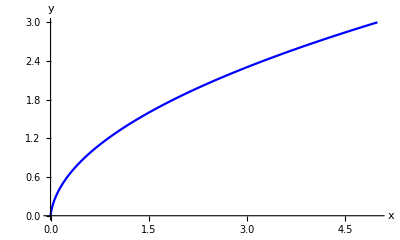

```mathematica
graf12  =ParametricPlot[Table[{x[t],y[t]}/.sol12],{t,0,t12},AxesLabel->{x,y},PlotRange->All,PlotStyle->{Blue}]
```

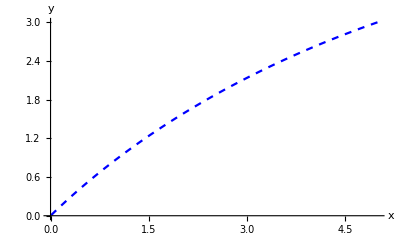

```mathematica
graf22  =ParametricPlot[Table[{x[t],y[t]}/.sol22],{t,0,t22},AxesLabel->{x,y},PlotRange->All,PlotStyle->{Blue,Dashed}]
```

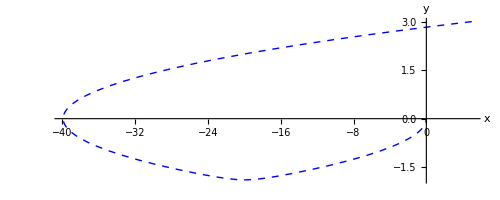

```mathematica
graf32  =ParametricPlot[Table[{x[t],y[t]}/.sol32],{t,0,t32},AxesLabel->{x,y},PlotRange->All,PlotStyle->{Blue,Dashed,Thick}]
```

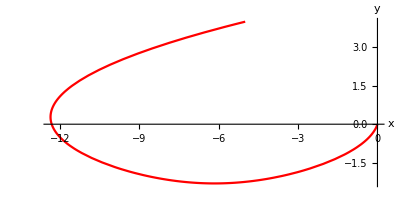

```mathematica
graf13  =ParametricPlot[Table[{x[t],y[t]}/.sol13],{t,0,t13},AxesLabel->{x,y},PlotRange->All,PlotStyle->{Red}]
```

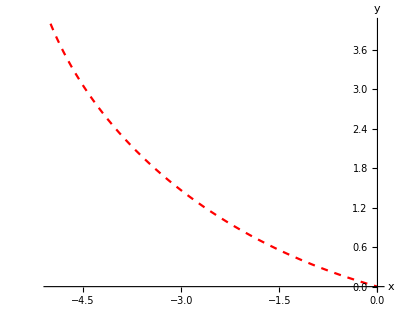

```mathematica
graf23  =ParametricPlot[Table[{x[t],y[t]}/.sol23],{t,0,t23},AxesLabel->{x,y},PlotRange->All,PlotStyle->{Red,Dashed}]
```

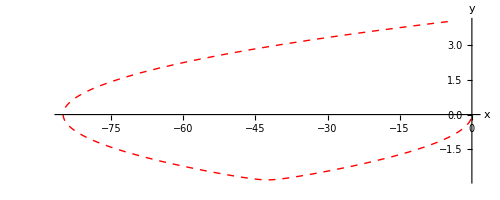

```mathematica
graf33  =ParametricPlot[Table[{x[t],y[t]}/.sol33],{t,0,t33},AxesLabel->{x,y},PlotRange->All,PlotStyle->{Red,Dashed,Thick}]
```

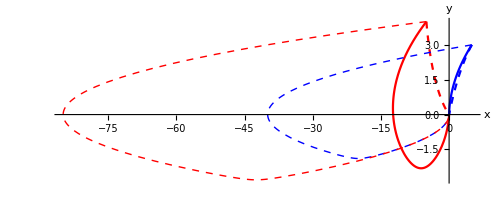

```mathematica
Show[graf12,graf13,graf22,graf23,graf32,graf33]
```

```mathematica
Tabulka0 = Table[{{5,4},{5,3},{-5,4}}]
```

{{5,4},{5,3},{-5,4}}

```mathematica
Tabulka1 = Table[{t11,t12,t13}]
```

{0.598308,0.303307,1.03978}

```mathematica
Tabulka2 = Table[{t21,t22,t23}]
```

{0.556139,0.515793,0.754895}

```mathematica
Tabulka3 = Table[{t31,t32,t33}]
```

{0.945912,0.697672,0.981379}

```mathematica
NumberForm[Grid[{{"Start X/Y","h = 1","h = 10","h = 0.1"},{TableForm[Tabulka0],TableForm[Tabulka1],TableForm[Tabulka2],TableForm[Tabulka3]}},Frame->All],7]
```

Start X/Y | h = 1 | h = 10 | h = 0.1
5 | 4
5 | 3
-5 | 4 | 0.598308
0.3033075
1.039785 | 0.5561394
0.5157925
0.7548947 | 0.9459117
0.6976717
0.9813792

```mathematica
Tabulka11=Table[{β[0]/.sol11,β[0]/.sol12,β[0]/.sol13}]
```

{{4.90294},{4.5281},{4.84961}}

```mathematica
Tabulka22=Table[{β[0]/.sol21,β[0]/.sol22,β[0]/.sol23}]
```

{{3.80173},{3.58315},{5.48133}}

```mathematica
Tabulka33=Table[{β[0]/.sol31,β[0]/.sol32,β[0]/.sol33}]
```

{{4.72725},{4.73243},{4.72687}}

```mathematica
NumberForm[Grid[{{"Start X/Y","h = 1","h = 10","h = 0.1"},{TableForm[Tabulka0],TableForm[Tabulka11],TableForm[Tabulka22],TableForm[Tabulka33]}},Frame->All],7]
```

Start X/Y | h = 1 | h = 10 | h = 0.1
5 | 4
5 | 3
-5 | 4 | 4.902939
4.528105
4.849607 | 3.801725
3.583146
5.481327 | 4.727247
4.73243
4.726865